```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
<<TheDiractionary`
```

### Check for Perfection

```mathematica
store=CloudGet["PerfectScrabbleGames"];
```

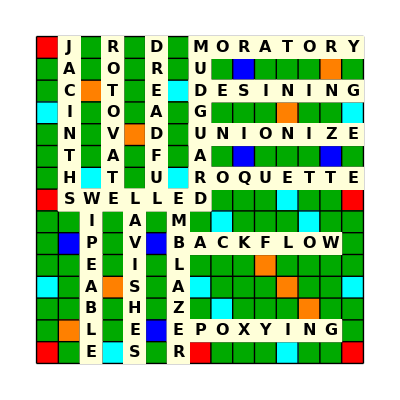

{True,Blanks: | {L,Z}
 Leftovers: | {E,I}}

```mathematica
game=RandomChoice[store];
board=CreateInitialScrabbleBoard[];
Show[board,Epilog->GameToEpilog[game]]
PerfectScrabbleGameQ[game]
Dataset[game]
```

```mathematica
PerfectScrabbleGameQ/@store
```

{{True,Blanks: | {H,N}
 Leftovers: | {J,P}},{True,Blanks: | {K,X}
 Leftovers: | {A,Q}},{True,Blanks: | {R}
 Leftovers: | {J}},{True,Blanks: | {A,I}
 Leftovers: | {B,E}},{True,Blanks: | {G,L}
 Leftovers: | {E,U}},{True,Blanks: | {O,T}
 Leftovers: | {A,F}},{True,Blanks: | {E,R}
 Leftovers: | {A,O}},{True,Blanks: | {C,I}
 Leftovers: | {E,W}},{True,Blanks: | {R}
 Leftovers: | {J}},{True,Blanks: | {H,R}
 Leftovers: | {A,J}},{True,Blanks: | {O,S}
 Leftovers: | {E,P}},{True,Blanks: | {R,R}
 Leftovers: | {E,W}},{True,Blanks: | {I,S}
 Leftovers: | {N,Z}},{True,Blanks: | {G,S}
 Leftovers: | {T,Y}},{True,Blanks: | {L,Z}
 Leftovers: | {E,I}}}

### GIF

```mathematica
gifFrame[1]=epilog[[1;;7]];
gifFrame[2]=epilog[[1;;15]];
gifFrame[3]=epilog[[1 ;; 23]];
gifFrame[4]=epilog[[1;; 31]];
gifFrame[5]=epilog[[1 ;; 39]];
gifFrame[6]=epilog[[1;; 47]];
gifFrame[7]=epilog[[1 ;; 55]];
gifFrame[8]=epilog[[1;; 63]];
gifFrame[9]=epilog[[1;; 71]];
gifFrame[10]=epilog[[1 ;; 79]];
gifFrame[11]=epilog[[1 ;; 87]];
gifFrame[12]=epilog[[1 ;; 95]];
gifFrame[13]=epilog[[1 ;; 103]];
gifFrame[14]=epilog[[1 ;; 111]];
```

```mathematica
Animate[Show[board,Epilog->gifFrame[i]],{i,1,14,1},AnimationRate->.5]
```

```mathematica
tileBag=StringJoin[KeyValueMap[Table[#1,#2]&,tiles[[All,"Quantity"]]]];
gifTiles[1]="AAAAAAAABBCCDDDDEEEEEEEEEEEFFGGHHIIIIIIIIJKLLLLMNNNNNNOOOOOOOOPPQRRRRRRSSTTTTTTUUUUVVWWXYYZ??";
gifTiles[2]="AAAAAAABBCCDDDDEEEEEEEEEEEFFGGHIIIIIIIJKLLLLMNNNNNNOOOOOOOOPQRRRRRRSTTTTTTUUUUVVXYYZ??";
gifTiles[3]="AAAAAAABBCCDDDDEEEEEEEEEEFFGGHIIIIIIJKLLLLMNNNNNOOOOOOPQRRRRRRTTTTTTUUUUVVXYY??";
gifTiles[4]="AAAAAAABBCDDDDEEEEEEEEEEFFGHIIIIIKLLLMNNNNNOOOOOPQRRRRRRTTTTTTUUUVVXYY??";
gifTiles[5]="AAAABBCDDDDEEEEEEEEEEFFGIIIIIKLLLMNNNOOOOOPQRRRRRRTTTTTTUUUVXYY??";
gifTiles[6]="AAAABBDDDDEEEEEEEEEFFIIIIIKLLMNNOOOOPQRRRRRRTTTTTTUUUVXY??";
gifTiles[7]="AAABBDDDDEEEEEEEEEFFIIIIKLLMNNOOPQRRRRTTTTTUUUVXY??";
gifTiles[8]="AABBDDDDEEEEEEEEEFFIIKLMNNOOPQRRRTTTTUUUVX??";
gifTiles[9]="ABBDDDDEEEEEEEEFFIKLMNNOOPQRTTUUUVX??";
gifTiles[10]="BBDDDEEEEEEEFFKLMNNOOPQUUUVX??";
gifTiles[11]="BDDEEEEEEFFLMOOPQUUVX??";
gifTiles[12]="DEEEELMOOPQUVX??";
gifTiles[13]="DEEEMPQU?";
gifTiles[14]="EP";
```

```mathematica
scrabbleAnimation=Animate[
  Grid[{
    {Style["Tiles Left: ",12]},
{Style[
If[StringLength[gifTiles[i]]>50,
StringInsert[gifTiles[i],"\n",50],
gifTiles[i]
],11]},(* Display the formatted gifTiles string *)
    {Show[board,Epilog->gifFrame[i],ImageSize->300]}  (* Display the board with the current frame *)
  }],
  {i,1,14.,1},
  AnimationRate->0.5
]
```

## To Do

Function for inserting a blank at position X

Function for generating Epilog and Tiles state to be animated.